```mathematica
qn[q1_,n_,α_]:=q1 * (1 - α)^(n-1)
```

```mathematica
pn[q1_,n_,α_]:=1-qn[q1,n,α]
```

```mathematica
p1 = pn[q1,1,α]
```

1-q1

```mathematica
p2=pn[q1,2,α]
```

1-q1 (1-α)

```mathematica
p3=pn[q1,3,α]
```

1-q1 (1-α)^2

```mathematica
(* p3g = 1 - (1-pn[q1,3,α]) *)
```

```mathematica
p3g = pn[q1,2,α] + qn[q1,2,α]*pn[q1,3,α]//FullSimplify
```

1+q1^2 (-1+α)^3

```mathematica
Bin[n_,k_,p_]:=PDF[BinomialDistribution[n,p],k]
```

```mathematica
m11 = ∑_(i=0)^3 i *Bin[3,i,p1]//FullSimplify
```

3-3 q1

```mathematica
m12 = Bin[3,1,p1]//FullSimplify
```

-3 (-1+q1) q1^2

```mathematica
m16 = Bin[3,2,p1]//FullSimplify
```

3 (-1+q1)^2 q1

```mathematica
m18 = Bin[3,3,p1]//FullSimplify
```

(1-q1)^3

```mathematica
m21 = ∑_(i=0)^2 i *Bin[2,i,p2] //FullSimplify
```

2+2 q1 (-1+α)

```mathematica
m31  = ∑_(i=0)^1 i *Bin[1,i,p3]//FullSimplify
```

1-q1 (-1+α)^2

```mathematica
m61 = ∑_(i=0)^1 i *Bin[1,i,p3g]//FullSimplify
```

1+q1^2 (-1+α)^3

```mathematica
m23 = Bin[1,1,p2]//FullSimplify
```

1+q1 (-1+α)

```mathematica
m25 = Bin[2,2,p2]//FullSimplify
```

(1+q1 (-1+α))^2

```mathematica
m34 = Bin[1,1,p3]//FullSimplify
```

1-q1 (-1+α)^2

```mathematica
m67 = Bin[1,1,p3g]//FullSimplify
```

1+q1^2 (-1+α)^3

```mathematica
M = ({{m11, m12, 0, 0, 0, m16, 0, m18}, {m21, 0, m23, 0, m25, 0, 0, 0}, {m31, 0, 0, m34, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {m61, 0, 0, 0, 0, 0, m67, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})
```

{{3-3 q1,-3 (-1+q1) q1^2,0,0,0,3 (-1+q1)^2 q1,0,(1-q1)^3},{2+2 q1 (-1+α),0,1+q1 (-1+α),0,(1+q1 (-1+α))^2,0,0,0},{1-q1 (-1+α)^2,0,0,1-q1 (-1+α)^2,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1+q1^2 (-1+α)^3,0,0,0,0,0,1+q1^2 (-1+α)^3,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
M/.{q1->4/5}//MatrixForm//FullSimplify
```

(3/5 | 48/125 | 0 | 0 | 0 | 12/125 | 0 | 1/125
2/5 (1+4 α) | 0 | 1/5 (1+4 α) | 0 | 1/25 (1+4 α)^2 | 0 | 0 | 0
1-4/5 (-1+α)^2 | 0 | 0 | 1-4/5 (-1+α)^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1+16/25 (-1+α)^3 | 0 | 0 | 0 | 0 | 0 | 1+16/25 (-1+α)^3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Eigenvalues[M]
```

{0,0,0,0,0,Root[-3 q1^2+9 q1^3-9 q1^4+3 q1^5-9 q1^3 α+18 q1^4 α-9 q1^5 α+3 q1^3 α^2-12 q1^4 α^2+9 q1^5 α^2+3 q1^4 α^3-3 q1^5 α^3+(-3 q1+12 q1^3-12 q1^4+3 q1^5-15 q1^3 α+24 q1^4 α-9 q1^5 α+9 q1^3 α^2-18 q1^4 α^2+9 q1^5 α^2-3 q1^3 α^3+6 q1^4 α^3-3 q1^5 α^3) #1+(-3+3 q1) #1^2+#1^3&,1],Root[-3 q1^2+9 q1^3-9 q1^4+3 q1^5-9 q1^3 α+18 q1^4 α-9 q1^5 α+3 q1^3 α^2-12 q1^4 α^2+9 q1^5 α^2+3 q1^4 α^3-3 q1^5 α^3+(-3 q1+12 q1^3-12 q1^4+3 q1^5-15 q1^3 α+24 q1^4 α-9 q1^5 α+9 q1^3 α^2-18 q1^4 α^2+9 q1^5 α^2-3 q1^3 α^3+6 q1^4 α^3-3 q1^5 α^3) #1+(-3+3 q1) #1^2+#1^3&,2],Root[-3 q1^2+9 q1^3-9 q1^4+3 q1^5-9 q1^3 α+18 q1^4 α-9 q1^5 α+3 q1^3 α^2-12 q1^4 α^2+9 q1^5 α^2+3 q1^4 α^3-3 q1^5 α^3+(-3 q1+12 q1^3-12 q1^4+3 q1^5-15 q1^3 α+24 q1^4 α-9 q1^5 α+9 q1^3 α^2-18 q1^4 α^2+9 q1^5 α^2-3 q1^3 α^3+6 q1^4 α^3-3 q1^5 α^3) #1+(-3+3 q1) #1^2+#1^3&,3]}

```mathematica
λmax2 = Eigenvalues[M][[6]]
```

Root[-3 q1^2+9 q1^3-9 q1^4+3 q1^5-9 q1^3 α+18 q1^4 α-9 q1^5 α+3 q1^3 α^2-12 q1^4 α^2+9 q1^5 α^2+3 q1^4 α^3-3 q1^5 α^3+(-3 q1+12 q1^3-12 q1^4+3 q1^5-15 q1^3 α+24 q1^4 α-9 q1^5 α+9 q1^3 α^2-18 q1^4 α^2+9 q1^5 α^2-3 q1^3 α^3+6 q1^4 α^3-3 q1^5 α^3) #1+(-3+3 q1) #1^2+#1^3&,1]

```mathematica
eqn2 = Series[λmax,{α, 0.14,1}]//Normal
```

2 (1-q1+√(1-q1-0.86 q1^2+0.86 q1^3))+((q1^2-q1^3) (-0.14+α))/(√(1-q1-0.86 q1^2+0.86 q1^3))

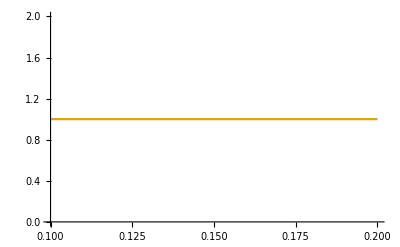

```mathematica
Plot[{eqn2,1},{α,0.1,.2}]
```

```mathematica
Solve[eqn2==1,α]/.{q1->0.8}
```

{{α→0.140625}}

```mathematica
ListPlot[data]
```

```mathematica
λmax/.{q1->0.8,α->0.195}
```

1.00217

```mathematica
λmax2=-3 q1^2+9 q1^3-9 q1^4+3 q1^5-9 q1^3 α+18 q1^4 α-9 q1^5 α+3 q1^3 α^2-12 q1^4 α^2+9 q1^5 α^2+3 q1^4 α^3-3 q1^5 α^3+(-3 q1+12 q1^3-12 q1^4+3 q1^5-18 q1^3 α+30 q1^4 α-12 q1^5 α+18 q1^3 α^2-36 q1^4 α^2+18 q1^5 α^2-12 q1^3 α^3+24 q1^4 α^3-12 q1^5 α^3+3 q1^3 α^4-6 q1^4 α^4+3 q1^5 α^4) #1+(-3+3 q1) #1^2+#1^3/.#1-> x
```

-3 q1^2+9 q1^3-9 q1^4+3 q1^5+(-3+3 q1) x^2+x^3-9 q1^3 α+18 q1^4 α-9 q1^5 α+3 q1^3 α^2-12 q1^4 α^2+9 q1^5 α^2+3 q1^4 α^3-3 q1^5 α^3+x (-3 q1+12 q1^3-12 q1^4+3 q1^5-18 q1^3 α+30 q1^4 α-12 q1^5 α+18 q1^3 α^2-36 q1^4 α^2+18 q1^5 α^2-12 q1^3 α^3+24 q1^4 α^3-12 q1^5 α^3+3 q1^3 α^4-6 q1^4 α^4+3 q1^5 α^4)

```mathematica
Solve[λmax2==0,{x}]/.{q1->0.9,α->0.1}
```

{{x→0.538249},{x→-0.119124+0.0951593 ⅈ},{x→-0.119124-0.0951593 ⅈ}}

```mathematica
Solve[λmax2==0,{x}][[1]]~
```

{x→1-q1-(2^(1/3) (-9+9 q1-9 q1^2+36 q1^3-36 q1^4+9 q1^5-54 q1^3 α+90 q1^4 α-36 q1^5 α+54 q1^3 α^2-108 q1^4 α^2+54 q1^5 α^2-36 q1^3 α^3+72 q1^4 α^3-36 q1^5 α^3+9 q1^3 α^4-18 q1^4 α^4+9 q1^5 α^4))/(3 (54-81 q1+162 q1^2-621 q1^3+891 q1^4-486 q1^5+81 q1^6+729 q1^3 α-1782 q1^4 α+1377 q1^5 α-324 q1^6 α-567 q1^3 α^2+1782 q1^4 α^2-1701 q1^5 α^2+486 q1^6 α^2+324 q1^3 α^3-1053 q1^4 α^3+1053 q1^5 α^3-324 q1^6 α^3-81 q1^3 α^4+243 q1^4 α^4-243 q1^5 α^4+81 q1^6 α^4+√(4 (-9+9 q1-9 q1^2+36 q1^3-36 q1^4+9 q1^5-54 q1^3 α+90 q1^4 α-36 q1^5 α+54 q1^3 α^2-108 q1^4 α^2+54 q1^5 α^2-36 q1^3 α^3+72 q1^4 α^3-36 q1^5 α^3+9 q1^3 α^4-18 q1^4 α^4+9 q1^5 α^4)^3+(54-81 q1+162 q1^2-621 q1^3+891 q1^4-486 q1^5+81 q1^6+729 q1^3 α-1782 q1^4 α+1377 q1^5 α-324 q1^6 α-567 q1^3 α^2+1782 q1^4 α^2-1701 q1^5 α^2+486 q1^6 α^2+324 q1^3 α^3-1053 q1^4 α^3+1053 q1^5 α^3-324 q1^6 α^3-81 q1^3 α^4+243 q1^4 α^4-243 q1^5 α^4+81 q1^6 α^4)^2))^(1/3))+1/(3 2^(1/3))(54-81 q1+162 q1^2-621 q1^3+891 q1^4-486 q1^5+81 q1^6+729 q1^3 α-1782 q1^4 α+1377 q1^5 α-324 q1^6 α-567 q1^3 α^2+1782 q1^4 α^2-1701 q1^5 α^2+486 q1^6 α^2+324 q1^3 α^3-1053 q1^4 α^3+1053 q1^5 α^3-324 q1^6 α^3-81 q1^3 α^4+243 q1^4 α^4-243 q1^5 α^4+81 q1^6 α^4+√(4 (-9+9 q1-9 q1^2+36 q1^3-36 q1^4+9 q1^5-54 q1^3 α+90 q1^4 α-36 q1^5 α+54 q1^3 α^2-108 q1^4 α^2+54 q1^5 α^2-36 q1^3 α^3+72 q1^4 α^3-36 q1^5 α^3+9 q1^3 α^4-18 q1^4 α^4+9 q1^5 α^4)^3+(54-81 q1+162 q1^2-621 q1^3+891 q1^4-486 q1^5+81 q1^6+729 q1^3 α-1782 q1^4 α+1377 q1^5 α-324 q1^6 α-567 q1^3 α^2+1782 q1^4 α^2-1701 q1^5 α^2+486 q1^6 α^2+324 q1^3 α^3-1053 q1^4 α^3+1053 q1^5 α^3-324 q1^6 α^3-81 q1^3 α^4+243 q1^4 α^4-243 q1^5 α^4+81 q1^6 α^4)^2))^(1/3)}

```mathematica
sol=Solve[λmax2==0,{x}][[1]][[1]][[2]];
```

### Solve the simple problem

```mathematica
eqn=Series[λmax/.{q1->0.8},{α,(0.173),1}]//Normal
```

0.986158+0.736928 (-0.173+α)

```mathematica
Solve[eqn == 1,α]
```

{{α→0.191783}}

```mathematica
λmax/.{q1->0.8,α->0.187}
```

1.00062